Average density on Earth is

```mathematica
ρ0 = 5515; (*kg/m3 = M/((4π)/3 R^3) *)
```

where the radius is

```mathematica
R=6.371 10^3;(*km*)
```

Density in the surface is

```mathematica
ρR =1000;(*kg/m3*)
```

then ρ_0 = 5.515 ρ_R. 
Total mass in the Earth is

M_T = 4π ∫_0^R ρ(r)r^2 ⅆr

acceleration in the surface is

```mathematica
g = 9.81 ;(*m/s2*)
```

Assuming now that the mass density profile inside the Earth is of the form

ρ(r) = ρ_av b (1 - c r/R)^d

being b,c,d parameters to determine. It can be written in the code as the function

```mathematica
ρ1[r_,b_,c_,d_]:=ρ0 b Power[1-c r/R,d]
```

this density have the following forms

```mathematica
Manipulate[Plot[ρ1[r,b,c,d],{r,0,R},PlotStyle-> RGBColor[b,c,d]],{b,0.2,4,0.2},{c,0.1,1,0.1},{d,0.1,1,0.1}]
```

Plot::plln: Limiting value Global`R in {Global`r,0,Global`R} is not a machine-sized real number.

Now, we have the next conditions to determine parameters b,c,d.

ρ(r = R) = b ρ_0(1-c )^d = ρ_R
		      b (1-c )^d = ρ_R/ρ_0=0.1813

The second conditions is given from the total mass, we must have

M_T = 4π ∫_0^R ρ(r)r^2 ⅆr = 4π ρ_0 b∫_0^R (1 - c r/R)^d r^2 ⅆr

Doing the integral in Mathematica gives

```mathematica
Integrate[b*x^2*(1-c*(x/R))^d,{x,0,R}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {2.37325,0,6371.}.

∫_0^6371. 13.364ⅆ2.37325

we have therefore the second condition:

3 b [ 2 -  (1-c)^(d+1)(2+2c(1+d)+c^2(2+3d + d^2))]=  c^3(6 + 11d + 6 d^2+ d^3)

As we want to approximate PREM density, let’s suppose d=0.6, then the other variables give

```mathematica
k=0.6;
Remove[x,y];
NSolve[x*(1-y)^k==0.1813&& x*(6-3*(1-y)^(k+1)*(2+2*y*(1+k)+y^2*(2+3*k+k^2)))==(y^3*(6+11*k+6*k^2+k^3)),{x,y}]
```

{{x→2.40802,y→0.986576},{x→0.1813,y→0.},{x→0.1813,y→0.},{x→0.1813,y→0.}}

This exponent was used in such a way that the density in the center coincides the better with that of prem:

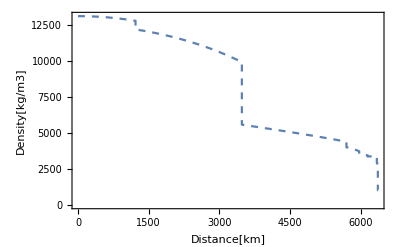

```mathematica
data=Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/prem-density.csv","Table"];
density prem=ListLinePlot[data,
PlotStyle->Dashed,
Frame->True,
FrameLabel->{{"Density[kg/m3]",None},{"Distance[km]",None}}]
```

the effective function with this parameter looks

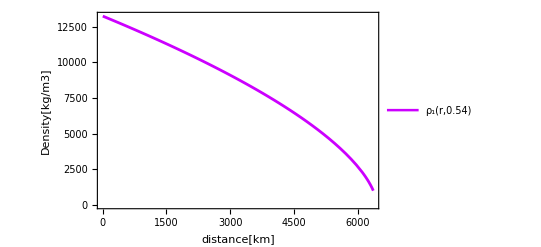

```mathematica
EffctiveFunction1=Plot[{ρ1[x,2.4,0.9865,0.6]},{x,0,R},
PlotLegends->Placed[{"ρ_1(r,0.54)"},{Right,Top}],
PlotStyle->{Thickness[0.005],Hue[0.8]},
Frame->True,
FrameLabel->{{"Density[kg/m3]",None},{"distance[km]",None}}]
```

We can now plot them together.

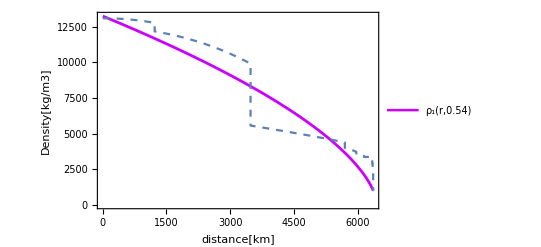

```mathematica
Show[EffctiveFunction1,density prem]
```

Let’s include, however, the value on the center as a third conditions to solve the system

ρ(0)=ρ_0 b =13088.5

then

```mathematica
b=13088.5/ρ0
```

2.37325

the  system to solve is now

(1-c)^d=0.1813/2.37325 = 0.076393
7.1197 [ 2 -  (1-c)^(d+1)(2+2c(1+d)+c^2(2+3d + d^2))]=  c^3(6 + 11d + 6 d^2+ d^3)

this would be the code on Mathematica to solve the system, but it takes too long

```mathematica
Remove[x,y];
NSolve[{(1-x)^y==0.0763,7.1197(2-(1-x)^(y+1)*(2+2*x*(1+y)+x^2*(2+3*y+x^2)))/(x^3*(6+11*y+6*y^2+y^3))==1},{x,y}]
```

On the other hand, the next code on Python finds the answer in a few seconds:

from scipy.optimize import root

def equations(p):
	x, y  = p
	eq1 = (1-x)**y - 0.0763
	eq2 = 7.12*(2 - (1 - x)**(y + 1)*(2 + 2*x*(1 + y) + x**2*(2 + 3*y + y**2))) / (x**3*(6 + 11*y + 6*y**2 + y**3)) - 1
	return ( eq1 , eq2 )
	
sol =  root(equations, (0.1, 0.1), method='lm', jac=None, tol=None, callback=None, options={'col_deriv': 0, 'xtol': 1.49012e-08, 'ftol': 1.49012e-08, 'gtol': 0.0, 'maxiter': 0, 'eps': 0.0, 'factor': 100, 'diag': None})


x = sol.x[0]
y = sol.x[1]

print(equations((x, y)))
print(x)
print(y)

x = 0.9875151202043234
y = 0.5867499795022912

Plotting with this result gives

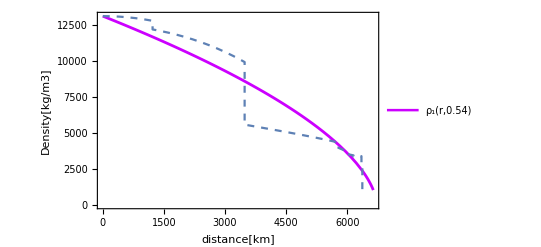

```mathematica
EffctiveFunction2=Plot[{ρ1[x,2.3732,0.9875,0.58]},{x,0,R},
PlotLegends->Placed[{"ρ_1(r,0.54)"},{Right,Top}],
PlotStyle->{Thickness[0.005],Hue[0.8]},
Frame->True,
FrameLabel->{{"Density[kg/m3]",None},{"distance[km]",None}}];
Show[EffctiveFunction2,density prem]
```

The density function to work from here on is then

```mathematica
b = 2.37325;
c = 0.9875;
d = 0.5867;
ρ[r_]:=ρ1[r,b,c,d]
```

```mathematica
Numerical checks
```

Mass

```mathematica
M[r_]:= 4 π  10^9 NIntegrate[ρ[x] x^2,{x,0,r}]
```

Total mass

```mathematica
M[R]
```

5.97603×10^24

Distribution inside the planet

```mathematica
Masses = Plot[{M[r]},{r,0,R},
PlotLegends->Placed[{"ρ_1(r,0.54)","ρ_2(r,0.55,4.26)"},{Right,Top}],
PlotStyle->{{Thickness[0.004],Pink},
Frame->True,
FrameLabel->{{"Mass(r) [kg]",None},{"r [km]",None}}]
```

-Graphics-

Acceleration of gravity

Computation of the acceleration inside the planet

```mathematica
Integrate[b*x^2*(1-c*(x/R))^d,{x,0,r}]
```

ConditionalExpression[(b (2 R^3+(1-(c r)/R)^d (c r-R) (c^2 (1+d) (2+d) r^2+2 c (1+d) r R+2 R^2)))/(c^3 (1+d) (2+d) (3+d)),Re[R/(c r)]>1||Re[R/(c r)]<0||R/(c r)∉Reals]

```mathematica
G = 6.674 10^-11;
a[r_]:=4 Pi 10^3 G  NIntegrate[ρ[x] x^2,{x,0,r}]/r^2
```

```mathematica
a[R]
```

9.8237

```mathematica
gravity prem = Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/gravity_prem.csv","Table"];
g prem=Interpolation[gravity prem,InterpolationOrder->5]
```

InterpolatingFunction[…]

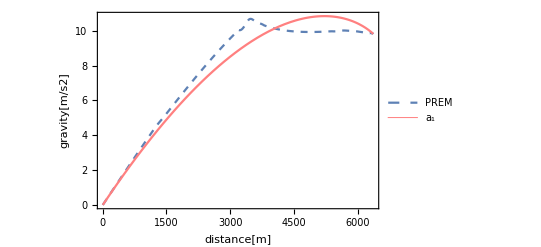

```mathematica
accelerations = Plot[{g prem[r],a[r]},{r,0,R},
PlotLegends->Placed[{"PREM","a_1"},{Right,Bottom}],
PlotStyle->{Dashed,{Thickness[0.004],Pink}},
Frame->True,
FrameLabel->{{"gravity[m/s2]",None},{"distance[m]",None}}]
```

#### Predictions

Velocity

```mathematica
Integrate[(2*R^3+(1-c*x/R)^d*(c*x-R)*(2*R^2+2*c*(1+d)*R*x+c^2*(2+3*d+d^2)*x^2))/x^2,{x,R,r}]
```

ConditionalExpression[-(-2+(1-c)^(2+d) (2+c+c d)) R^2+(-2 R^3+(1-(c r)/R)^d (-c r+R)^2 (c (1+d) r+2 R))/r,((Im[c] (Im[R]^2+Re[R]^2))/(Re[c] (Im[R] Re[r]-Im[r] Re[R])+Im[c] (-Im[r] Im[R]+Im[R]^2-Re[r] Re[R]+Re[R]^2))≥1||(Im[r] Re[c] Re[R]+Im[c] (Im[r] Im[R]+Re[r] Re[R])≥Im[R] Re[c] Re[r]+Im[c] (Im[R]^2+Re[R]^2)&&(Im[c] (Im[R]^2+Re[R]^2)≥0||Im[c] (Im[R]^2-Im[c] Im[R] Re[r]+Re[R] (-Re[r]+Re[R])+Im[r] (-Im[R]+Im[c] Re[R]))≤(-1+Re[c]) Re[c] (Im[R] Re[r]-Im[r] Re[R])))||(Im[r] Re[c] Re[R]+Im[c] (Im[r] Im[R]+Re[r] Re[R])≤Im[R] Re[c] Re[r]+Im[c] (Im[R]^2+Re[R]^2)&&(Im[c] (Im[R]^2+Re[R]^2)≤0||Im[c] (Im[R]^2-Im[c] Im[R] Re[r]+Re[R] (-Re[r]+Re[R])+Im[r] (-Im[R]+Im[c] Re[R]))≥(-1+Re[c]) Re[c] (Im[R] Re[r]-Im[r] Re[R]))))&&(R/(r-R)∉Reals||Re[R/(r-R)]<-1||(R/(r-R)≠0&&Re[R/(r-R)]≥0))&&(((Re[(R-c R)/(c r-c R)]≥1||Re[(R-c R)/(c r-c R)]≤0)&&((-1+c) R)/(c (r-R))∉Reals)||(R-c R)/(c r-c R)∉Reals||Re[(R-c R)/(c r-c R)]>1||Re[(R-c R)/(c r-c R)]<0)]

```mathematica
vprem[r_?NumberQ] := 10^(3/2)Sqrt[2*NIntegrate[g prem[x],{x,r,R}]]
v[r_?NumberQ] := Sqrt[2*4 Pi  10^6  G  NIntegrate[  ρ[x] x^2 /y^2,{y,r,R},{x,0,y}]]
```

```mathematica
{v[R],v[0], vprem[0]}
```

{0.,9842.53,9914.73}

Check of times for constant density case

```mathematica
Integrate[1/Sqrt[R^(2)-x^(2)],{x,0,R}]
```

ConditionalExpression[π/2,Re[R]>0&&Im[R]==0]

Traversal times for chord path.

```mathematica
Remove[c,d,R];
Integrate[1/Sqrt[(2+(1-c)^{2+d}*(2+c+c*d))*R^2-(2*R/x+(1-c*x/R)^{2+d}*(2*R/x+c+c*d))],{x,0,R}]
```

```mathematica
Remove[c,k,R,x];
Integrate[1/Sqrt[1-(1/k)*(2*R/x-(1-c*x/R)^2)],{x,0,R}]
```

∫_0^R 1/(√(1-((2 R)/x-(1-(c x)/R)^2)/k))ⅆx

```mathematica
Tprem = 10^3 NIntegrate[1/vprem[x],{x,0,R}]/30
Teff =  10^3 NIntegrate[1/v[x],{x,0,R}]/30
```

38.1875

37.7428

```mathematica
Error = (Tprem - Teff)/Tprem * 100
```

1.16436